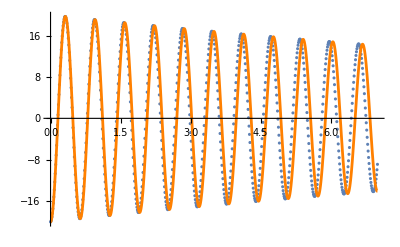

```mathematica
{m,k,d,y0,TMax}={1,100,0.1,0.2,7};
ySol=NDSolveValue[{
m y''[t]==-k y[t] - d y'[t],y[0]==y0,y'[0]==0.0},
y,{t, 0, TMax}];
Data=Table[{t, ySol''[t]},{t, 0, TMax, 0.01}];
Show[
ListPlot[Data],
Plot[-20 Cos[ 11/7 2π t] E^(-d/(2 m) t), {t, 0, 7},
PlotStyle->Orange]
]
```

```mathematica
d/(2m)
2π 11/6.9
```

0.05

10.0167

{ω→10.001,r→0.0499952}

-20 ⅇ^(-0.0499952 t) Cos[10.001 t]

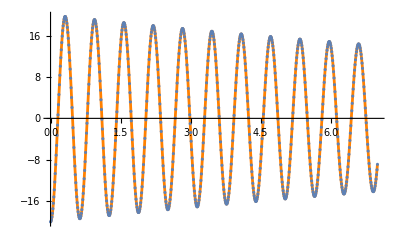

```mathematica
Clear[yFit]
Data=Table[{t, ySol''[t]},{t, 0, TMax, 0.01}];
fit=FindFit[Data,-20 Cos[ω t] E^(-r t),{ω,r},t]
yFit[t_]=-20 Cos[ω t] E^(-r t)/.fit
Show[
Plot[yFit[t], {t, 0, 7},
PlotStyle->Orange],
ListPlot[Data]
]
```

{a0→1.,ω→10.0007,r→0.0486183}

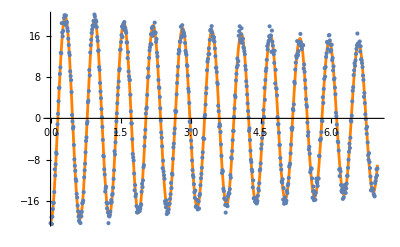

```mathematica
Clear[yFit]
ϵ = 1;
Data=Table[{t, ySol''[t]+ ϵ RandomVariate[NormalDistribution[0,1]] },{t, 0, TMax, 0.01}];
fit=FindFit[Data,-20 Cos[ω t] E^(-r t),{a0,ω,r},t]
yFit[t_]=-20 Cos[ω t] E^(-r t)/.fit ;
Show[
Plot[yFit[t], {t, 0, 7},
PlotStyle->Orange],
ListPlot[Data]
]
```

```mathematica
?FindFit
```

```mathematica
Length[Data]
```

701

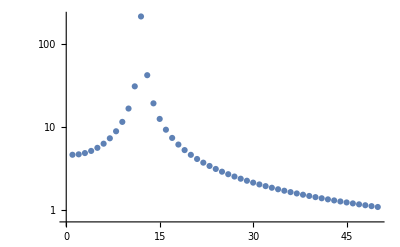

```mathematica
FData=Fourier[Data];
ListLogPlot[Abs[FData]⟦1;;50⟧,
PlotRange->All]
```

```mathematica
1/200.
```

0.005

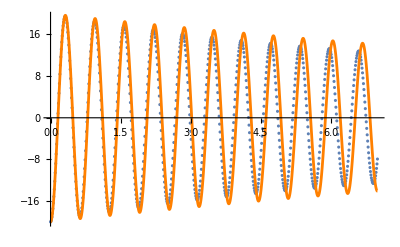

```mathematica
{m,k,d,y0,TMax}={1,100,0.1,0.2,7};
ySol=NDSolveValue[{
m y''[t]==-k y[t] - d y'[t]*Abs[y'[t]],y[0]==y0,y'[0]==0.0},
y,{t, 0, TMax}];
Data=Table[{t, ySol''[t]},{t, 0, TMax, 0.01}];
Show[
ListPlot[Data],
Plot[-20 Cos[ 11/7 2π t] E^(-d/(2 m) t), {t, 0, 7},
PlotStyle->Orange]
]
```

{ω→10.0012,r→0.0709268}

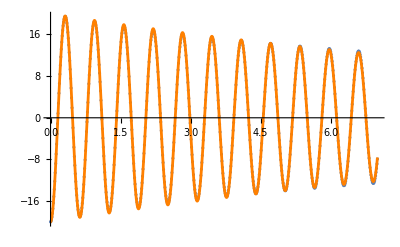

```mathematica
{m,k,d,y0,TMax}={1,100,0.1,0.2,7};
ySol=NDSolveValue[{
m y''[t]==-k y[t] - d y'[t]*Abs[y'[t]],y[0]==y0,y'[0]==0.0},
y,{t, 0, TMax}];
Data=Table[{t, ySol''[t]},{t, 0, TMax, 0.01}];
fit=FindFit[Data,-20 Cos[ω t] E^(-r t),{ω,r},t]
yFit[t_]=-20 Cos[ω t] E^(-r t)/.fit ;
Show[
ListPlot[Data],
Plot[yFit[t], {t, 0, 7},
PlotStyle->Orange]
]
```

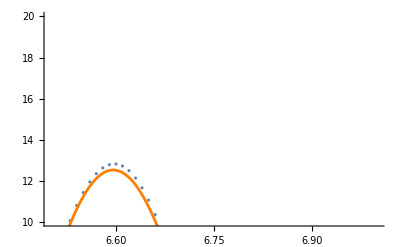

```mathematica
Show[
ListPlot[Data],
Plot[yFit[t], {t, 0, 7},
PlotStyle->Orange],
PlotRange->{{6.5,7},{10,20}}
]
```

```mathematica
0.5/12
```

0.0416667

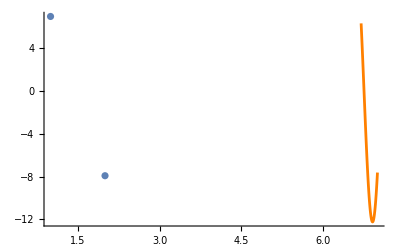

```mathematica
Show[
ListPlot[Data⟦-300;-1⟧],
Plot[yFit[t], {t, 6.7, 7},
PlotStyle->Orange],
PlotRange->All
]
```